{{y[t]→InterpolatingFunction[…][t]}}

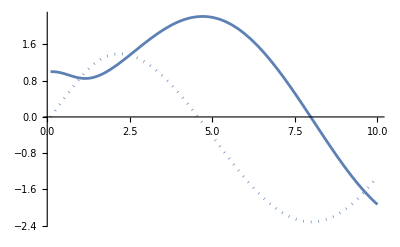

-Graphics-

```mathematica
ClearAll["Global`*"]
ClearAll[Derivative]

k := 1
m := 1
L := 1

(*Define the time-dependent coefficients*)
T[t_]:=  1+L^2/t^2
Tinv[t_]:= 1/T[t]
gam[t_]:= -4*(L^2/t^3)*Tinv[t]

eps := 0.1
Tmax := 10
 
numsol = NDSolve[{T[t]*(gam[t] - 2*I*m)*y'[t]+(Tinv[t]*k^2-I*m*T[t]*gam[t]+(1-T[t])*m^2)*y[t]== 0, y[eps]==1}, y[t], {t,eps,Tmax}]

ReImPlot[Evaluate[y[t]/. numsol],{t,eps,Tmax},PlotRange->All]
AbsArgPlot[Evaluate[y[t]/. numsol],{t,eps,Tmax},PlotRange->All]
```